```mathematica
accuracygoal=16;
(* eqn (15) *)
deltaPhiSquare[b_, k_, la_, ns_]:= 1/(ns^2 Sqrt[2Pi])(ⅇ^(-(b+k)^2/2.) (b+k)-ⅇ^(-(b-la)^2/2) (b+2 k+la) +√(π/2) ((b+k)^2+1) Erf[(b+k)/(√2)]+√(π/2) ((b+k)^2+1) Erf[(-b+la)/(√2)]);
(*a more accurate formula for the case where input length is fixed as Sqrt[ns], the difference between the one above is ~1%*)
(*deltaPhiSquare[b_, k_, la_, ns_]:= NIntegrate[Gamma[ns/2]/(Sqrt[Pi ns](ns-1)Gamma[(ns-1)/2] ns)(1-x^2/ns)^((ns-1)/2)(k+b-x)^2, {x, b-la, b+k}];*)
```

```mathematica
(* eqn (25) *)
pActive[b_, k_, la_, ns_, mu0_, t_]:= 1/2 Erfc[1/Sqrt[2.] (b-mu0 Exp[-ns*t*deltaPhiSquare[b, k, la, ns]/2])/Sqrt[1-Exp[-ns*t*deltaPhiSquare[b, k, la, ns]]]];
```

```mathematica
(* eqn (11) *)
q[v_]:=1/2. Erfc[v/Sqrt[2.]];
(* eqn (12) *)
(*pLeftMargin[v_, nd_, R_]:=Exp[-v^2/2]/Sqrt[2Pi]*(nd!)/((nd-1-R nd)!(R nd)!)q[v]^(R nd)*(1-q[v])^(nd-1-R nd);*)
pLeftMargin[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/Sqrt[2Pi](1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));(*qv should always be q[v]*)
```

```mathematica
(* eqn (26) *)
PActiveNonInt[b_, k_, la_, ns_, t_]:=NIntegrate[1/Sqrt[2Pi] Exp[-mu0^2/2]pActive[b, k, la, ns, mu0, t], {mu0, -Infinity, b-la}, AccuracyGoal->accuracygoal]+NIntegrate[1/Sqrt[2Pi] Exp[-mu0^2/2]pActive[b, k, la, ns, mu0, t], {mu0, b+k, Infinity}, AccuracyGoal->accuracygoal]+
(q[b-la]-q[b+k])pActive[b, k, la, ns, b+k, t];
```

```mathematica
(* P1 in eqn (28), the two definitions of P1 below are equivalent, the first one is faster, but might give wrong result when nd is large (~10000) *)
PActiveInt1[b_, k_, R_, la_,ns_, nd_,t_]:=(1-R)NIntegrate[pLeftMargin[v, nd, R nd, q[v]](1/Sqrt[2.Pi] Exp[-mu0^2/2.]pActive[b, k, la, ns, mu0, t])/(1-q[v]), {v, -Infinity, Infinity}, {mu0, -Infinity, v}]; 
(*PActiveInt1[b_, k_, R_, la_,ns_, nd_,t_]:=((1-R)nd)/(nd-R nd -1) NIntegrate[pActive[b, k, la, ns, Sqrt[2.]InverseErfc[2qmu0], t], {x,0, 1.}, {qmu0, InverseBetaRegularized[x, R nd +1, nd -R nd-1], 1.}];*)
(* P2 in eqn (28) *)
PActiveInt2[b_, k_, R_, la_, ns_, nd_,t_]:= (R-q[b+k])HeavisideTheta[R-q[b+k]]*pActive[b, k, la, ns, b+k, t];
(* P3 in eqn (28) *)
PActiveInt3[b_, k_, R_, la_, ns_, nd_,t_]:=NIntegrate[1/Sqrt[2Pi] Exp[-mu0^2/2]pActive[b, k, la, ns, mu0, t], {mu0, b+k, Infinity}, AccuracyGoal->accuracygoal];
(* eqn (28) *)
PActiveInt[b_, k_, R_, la_, ns_, nd_,t_]:=PActiveInt1[b, k, R, la, ns, nd, t]+PActiveInt2[b, k, R, la, ns, nd, t]+PActiveInt3[b, k, R, la, ns, nd, t];(*always make sure that R=0.5*Erfc[(b-la)/Sqrt[2]]*)
```

```mathematica
(*probability that n dendrites are actitve, pa is the probability that one dendrite is active*)
PnActiveNonInt[nd_, n_, pa_]:=(1-pa)^nd/(n!)(∏_(m=0)^(n-1) (nd-m)pa/(1-pa));
(*Negative result probability. pa is the probability that one dendrite is active, recognition threshold is n0 (the number of active dendrites must be larger than n0) *)
PNegativeNonInt[nd_, n0_, pa_]:=∑_(n=0)^n0 PnActiveNonInt[nd, n, pa];
(*Approximation of PNegativeNonInt by treating binomial distribution like a gaussian distribution*)
PNegativeNonIntGaussian[nd_, n0_, pa_]:=1/2(1+Erf[(n0-pa nd)/Sqrt[2nd (pa-pa^2)]]);
```

```mathematica
(*probability that n dendrites are actitve, pa1 is the prob that an originally active dendrite is active, pa2 is the prob that an originally inactive dendrite is active*)
PnActiveInt[nd_, Rnd_, n_, pa1_, pa2_]:= (1-pa1)^Rnd(1-pa2)^(nd-Rnd)∑_(n1=0)^n (1/(n1! (n-n1)!)*(∏_(m1=0)^(n1-1) ((Rnd-m1)pa1)/(1-pa1)) * (∏_(m2=0)^(n-n1-1) ((nd-Rnd-m2)pa2)/(1-pa2)))
(*Negative result probability. Recognition threshold is n0 (the number of active dendrites must be larger than n0) *)
PNegativeInt[nd_, Rnd_, n0_, pa1_, pa2_]:=∑_(n=0)^n0 PnActiveInt[nd, Rnd, n, pa1, pa2];
(*Approximation of PNegativeInt by treating binomial distribution like a gaussian distribution*)
PNegativeIntGaussian[nd_, Rnd_, n0_, pa1_, pa2_]:=1/2(1+Erf[(n0-(Rnd pa1+(nd-Rnd)pa2))/(Sqrt[2]Sqrt[Rnd(pa1-pa1^2)+(nd-Rnd)(pa2-pa2^2)])]);
```

```mathematica
(********************************************************************************)
ns=400;nd=1000;ndR=15;ndb=3.5;ndk=0.4;n0=8;
R=ndR/nd;
b=InverseErfc[2*ndb/nd]Sqrt[2.];
la=InverseErfc[2*ndb/nd]Sqrt[2.]-InverseErfc[2*ndR/nd]Sqrt[2.];
k = InverseErfc[2*ndk/nd]Sqrt[2]-b;

decaySteps=10000 ;stepSpacing=100;
timeList = Table[t, {t, 1, decaySteps, stepSpacing}];
```

```mathematica
(********************************************************************************)
fp =PNegativeNonInt[nd*1.0, n0, ndb/nd]
```

0.990259

```mathematica
(********************************************************************************)
```

```mathematica
paNonIntList = Thread[PActiveNonInt[b, k, la, ns, timeList]];
pa1IntList = Thread[(PActiveInt2[b, k, R, la, ns, nd,timeList]+PActiveInt3[b, k, R, la, ns, nd,timeList])/R];
pa2IntList = Thread[PActiveInt1[b, k, R, la, ns, nd,timeList]/(1-R)];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

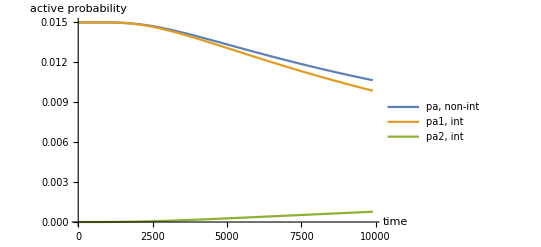

```mathematica
ListLinePlot[{Transpose[{timeList, paNonIntList}], Transpose[{timeList, pa1IntList*R}], Transpose[{timeList, pa2IntList*(1-R)}]}, AxesLabel->{"time", "active probability"}, PlotLegends->{"pa, non-int", "pa1, int", "pa2, int"}, PlotRange->All]
```

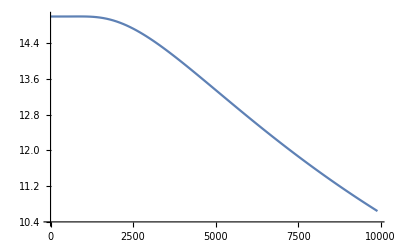

```mathematica
meanListInt = Transpose[{timeList, pa1IntList*ndR+pa2IntList*(nd-ndR)}];
ListLinePlot[meanListInt]
Export["mean_int.csv",meanListInt,"CSV"];
```

```mathematica
pNegativeNonIntList = Thread[PNegativeNonInt[nd, n0, paNonIntList]];
pNegativeIntList = Thread[PNegativeInt[nd, ndR, n0, pa1IntList, pa2IntList]];
pNegativeNonIntGaussianList = Thread[PNegativeNonIntGaussian[nd, n0, paNonIntList]];
pNegativeIntGaussianList = Thread[PNegativeIntGaussian[nd, ndR, n0, pa1IntList, pa2IntList]];
```

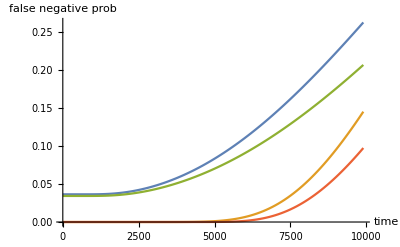

```mathematica
ListLinePlot[{Transpose[{timeList, pNegativeNonIntList}],Transpose[{timeList, pNegativeIntList}],Transpose[{timeList, pNegativeNonIntGaussianList}],Transpose[{timeList, pNegativeIntGaussianList}]}, AxesLabel->{"time", "false negative prob"}]
```

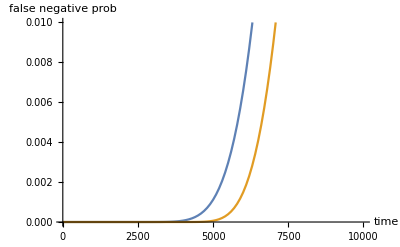

```mathematica
ListLinePlot[{Transpose[{timeList, pNegativeIntList}],Transpose[{timeList, pNegativeIntGaussianList}]}, AxesLabel->{"time", "false negative prob"}, PlotRange->{{0, 10000}, {0,0.01}}]
```

```mathematica
(******************************************* parameter optimization ************************************************)
```

```mathematica
nsnd=200*300;nd=300;ndR=15;ndb=3.5;ndk=0.4;n0=8;th=0.01; (*these are free parameters*)
ns=nsnd/nd;
b=InverseErfc[2*ndb/nd]Sqrt[2.];
la=InverseErfc[2*ndb/nd]Sqrt[2.]-InverseErfc[2*ndR/nd]Sqrt[2.];
k = InverseErfc[2*ndk/nd]Sqrt[2]-b;
tStart=850 ;tEnd=1000;dt=10;
tList = Table[t, {t, tStart, tEnd, dt}];
Fp99[nd_, ndb_, n0_] :=PNegativeNonInt[nd*1.0, n0, ndb/nd];
GetPNegativeListNonInt[ns_, nd_, b_, k_, la_, n0_, tList_]:=Thread[PNegativeNonInt[nd, n0,Thread[PActiveNonInt[b, k, la, ns, tList]]]];
GetPNegativeListInt[ns_, nd_, b_, k_, la_, ndR_,n0_, tList_]:=Thread[PNegativeInt[nd, ndR, n0, 
Thread[(PActiveInt2[b, k, ndR/nd, la, ns, nd,tList]+PActiveInt3[b, k, ndR/nd, la, ns, nd,tList])/(ndR/nd)], 
Thread[PActiveInt1[b, k,ndR/nd, la, ns, nd,tList]/(1-ndR/nd)]]];
GetCapcity[th_, pNegativeList_]:=(Position[Thread[And[Thread[pNegativeList[[2;;]]>=th],Thread[pNegativeList[[;;-2]]<th]]], True]*dt + tStart)//Flatten;
GetCapcityNonInt[ns_, nd_, b_, k_, la_, n0_, th_, tList_]:=GetCapcity[th, GetPNegativeListNonInt[ns, nd, b, k, la, n0, tList]];
GetCapcityInt[ns_, nd_, b_, k_, la_, ndR_, n0_, th_, tList_]:=GetCapcity[th, GetPNegativeListInt[ns, nd, b, k, la, ndR, n0, tList]];
```

```mathematica
(*************** optimize nd *************)
ndStart = 30; ndEnd=150; dnd=10;
ndList = Table[nd, {nd, ndStart, ndEnd, dnd}];
(******)
nsList = nsnd/ndList;
bList = InverseErfc[2*ndb/ndList]Sqrt[2.];
laList=InverseErfc[2*ndb/ndList]Sqrt[2.]-InverseErfc[2*ndR/ndList]Sqrt[2.];
kList = InverseErfc[2*ndk/ndList]Sqrt[2]-bList;
Table[{ndList[[i]], GetCapcityInt[nsList[[i]], ndList[[i]], bList[[i]], kList[[i]], laList[[i]], ndR, n0, th, tList]}, {i, 1, Length[ndList]}]
Table[{nd, Thread[Fp99[nd, ndb, n0]]}, {nd, ndList}]
```

{{30,{820}},{40,{840}},{50,{860}},{60,{880}},{70,{880}},{80,{900}},{90,{900}},{100,{900}},{110,{900}},{120,{920}},{130,{920}},{140,{920}},{150,{920}}}

{{30,0.994239},{40,0.993278},{50,0.992677},{60,0.992268},{70,0.991972},{80,0.991747},{90,0.991571},{100,0.99143},{110,0.991313},{120,0.991216},{130,0.991133},{140,0.991063},{150,0.991001}}

```mathematica
(*************** optimize nd *************)
ndStart = 50; ndEnd=5000; dnd=100;
ndList = Table[nd, {nd, ndStart, ndEnd, dnd}];
(******)
nsList = nsnd/ndList;
bList = InverseErfc[2*ndb/ndList]Sqrt[2.];
laList=InverseErfc[2*ndb/ndList]Sqrt[2.]-InverseErfc[2*ndR/ndList]Sqrt[2.];
kList = InverseErfc[2*ndk/ndList]Sqrt[2]-bList;
Table[{ndList[[i]], GetCapcityInt[nsList[[i]], ndList[[i]], bList[[i]], kList[[i]], laList[[i]], ndR, n0, th, tList]}, {i, 1, Length[ndList]}]
Table[{nd, Thread[Fp99[nd, ndb, n0]]}, {nd, ndList}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{50,{860}},{150,{910}},{250,{930}},{350,{930}},{450,{940}},{550,{940}},{650,{950}},{750,{950}},{850,{950}},{950,{950}},{1050,{950}},{1150,{950}},{1250,{950}},{1350,{950}},{1450,{960}},{1550,{960}},{1650,{960}},{1750,{960}},{1850,{960}},{1950,{960}},{2050,{960}},{2150,{960}},{2250,{960}},{2350,{960}},{2450,{960}},{2550,{960}},{2650,{960}},{2750,{960}},{2850,{960}},{2950,{960}},{3050,{960}},{3150,{960}},{3250,{960}},{3350,{960}},{3450,{930}},{3550,{930}},{3650,{930}},{3750,{930}},{3850,{930}},{3950,{930}},{4050,{930}},{4150,{930}},{4250,{930}},{4350,{930}},{4450,{930}},{4550,{930}},{4650,{930}},{4750,{930}},{4850,{930}},{4950,{930}}}

{{50,0.992677},{150,0.991001},{250,0.990654},{350,0.990504},{450,0.99042},{550,0.990367},{650,0.99033},{750,0.990303},{850,0.990282},{950,0.990266},{1050,0.990253},{1150,0.990242},{1250,0.990232},{1350,0.990225},{1450,0.990218},{1550,0.990212},{1650,0.990207},{1750,0.990202},{1850,0.990198},{1950,0.990194},{2050,0.990191},{2150,0.990188},{2250,0.990185},{2350,0.990183},{2450,0.990181},{2550,0.990178},{2650,0.990176},{2750,0.990175},{2850,0.990173},{2950,0.990171},{3050,0.99017},{3150,0.990168},{3250,0.990167},{3350,0.990166},{3450,0.990165},{3550,0.990164},{3650,0.990163},{3750,0.990162},{3850,0.990161},{3950,0.99016},{4050,0.990159},{4150,0.990158},{4250,0.990158},{4350,0.990157},{4450,0.990156},{4550,0.990156},{4650,0.990155},{4750,0.990154},{4850,0.990154},{4950,0.990153}}

```mathematica
(*************** optimize ndb *************)
ndbStart = 2.5; ndbEnd=4.5; dndb=0.5;
ndbList = Table[b, {b, ndbStart, ndbEnd, dndb}];
(******)
bList = InverseErfc[2*ndbList/nd]Sqrt[2.];
kList=InverseErfc[2*ndk/nd]Sqrt[2]-bList;
laList = InverseErfc[2*ndbList/nd]Sqrt[2.]-InverseErfc[2*ndR/nd]Sqrt[2.];
Table[{ndbList[[i]], GetCapcityInt[ns, nd, bList[[i]], kList[[i]], laList[[i]], ndR, n0, th, tList]}, {i, 1, Length[ndbList]}]
Table[{ndb, Thread[Fp99[nd, ndb, n0]]}, {ndb, ndbList}]
```

{{2.5,{}},{3.,{}},{3.5,{960}},{4.,{}},{4.5,{}}}

{{2.5,0.998868},{3.,0.996221},{3.5,0.990179},{4.,0.978732},{4.5,0.959889}}

```mathematica
(*************** optimize ndR *************)
ndRStart = 10; ndREnd=20; dndR=1;
ndRList = Table[ndR, {ndR, ndRStart, ndREnd, dndR}];
(******)
laList = InverseErfc[2*ndb/nd]Sqrt[2.]-InverseErfc[2*ndRList/nd]Sqrt[2.];
Table[{ndRList[[i]], GetCapcityInt[ns, nd, b, k, laList[[i]], ndRList[[i]], n0, th, tList]}, {i, 1, Length[ndRList]}]
```

{{10,{}},{11,{}},{12,{910}},{13,{940}},{14,{960}},{15,{960}},{16,{960}},{17,{950}},{18,{930}},{19,{920}},{20,{900}}}

```mathematica
(*************** optimize ndk *************)
ndkStart = 0.1; ndkEnd=0.6; dndk=0.1;
ndkList = Table[ndk, {ndk, ndkStart, ndkEnd, dndk}];
(******)
kList=InverseErfc[2*ndkList/nd]Sqrt[2]-b;
Table[{ndkList[[i]], GetCapcityInt[ns, nd, b, kList[[i]], la, ndR, n0, th, tList]}, {i, 1, Length[ndkList]}]
```

{{0.1,{900}},{0.2,{940}},{0.3,{960}},{0.4,{960}},{0.5,{960}},{0.6,{950}}}

```mathematica
kList
```

{0.955518,0.78613,0.683819,0.609665,0.551202,0.502794}

```mathematica
bList
```

{3.09023,3.03567,2.98888,2.94784,2.91124}

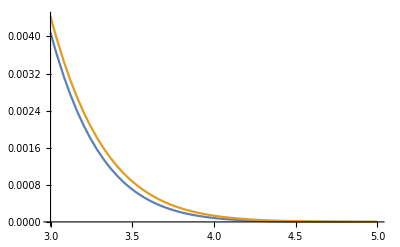

```mathematica
f[x_, n_]:=(1-x^2/n)^((n-3)/2)*Gamma[n/2]/(Gamma[(n-1)/2]Sqrt[Pi n]);
f2[x_, n_]:=Exp[- x^2/2]/Sqrt[2Pi];
Plot[{f[x, 100], f2[x, 100]}, {x, 3, 5}, PlotRange->All]
```

```mathematica
deltaPhiSquare[b, k, la, ns]
```

1.26617×10^-6

```mathematica
NIntegrate[Gamma[ns/2]/(Sqrt[Pi ns](ns-1)Gamma[(ns-1)/2] ns)(1-x^2/ns)^((ns-1)/2)(k+b-x)^2, {x, b-la, b+k}]
```

1.26617×10^-6

```mathematica
la
```

0.623079